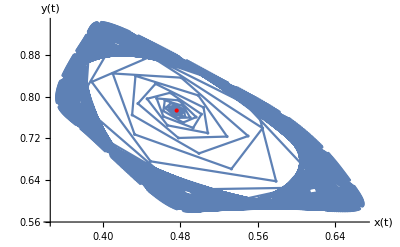

```mathematica
c=2.1;
r=3.1;
sol1=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,1,500}];
ListPlot[sol1,PlotRange->All,AxesLabel->{x[t],y[t]},Joined->True,Mesh->All,Epilog->{Red,,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

```mathematica
Clear[c]
```

```mathematica
Clear[r]
```

```mathematica
Solve[{x==(r+1)*x-r*x^2-c*x*y,y==c*x*y},{x,y}]
```

{{x→1/c,y→((-1+c) r)/c^2},{x→0,y→0},{x→1,y→0}}

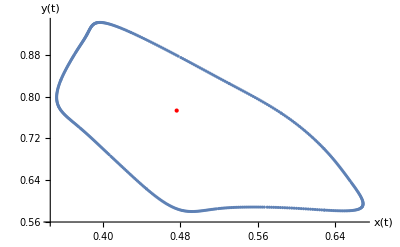

```mathematica
c=2.1;
r=3.1;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,10000,10500}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Epilog->{Red,,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

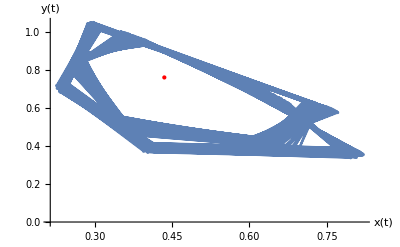

```mathematica
c=2.3;
r=3.1;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,10000,10500}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Joined->True,Mesh->All,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

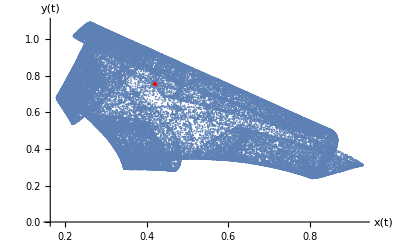

```mathematica
c=2.38;
r=3.1;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,10000,80000}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

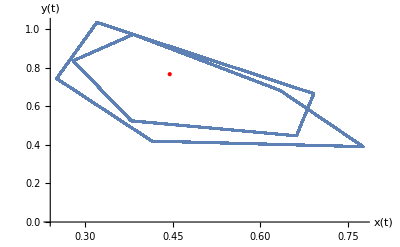

```mathematica
c=2.25;
r=3.1;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,10000,20000}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Joined->True,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

```mathematica
Clear[r]
```

```mathematica
Clear[c]
```

```mathematica
Tr[{{1-r*c,-1},{r-r/c,1}}]
```

2-c r

```mathematica
Det[{{1-r*c,-1},{r-r/c,1}}]
```

```mathematica
1+r-r/c-c r
CharacteristicPolynomial[{{1-r*c,-1},{r-r/c,1}},x]
```

1+r-r/c-c r

1+r-r/c-c r-2 x+c r x+x^2

Siempre se cumple
condición dos




condición tres

```mathematica
FullSimplify[4*c/(2*c^2+1-c)]
```

(4 c)/(1+c (-1+2 c))

```mathematica
(4 c)/(1+c (-1+2 c))/.{c->1.1}
```

1.89655

```mathematica
4*c/(3-c)/.{c->1.1}
```

2.31579

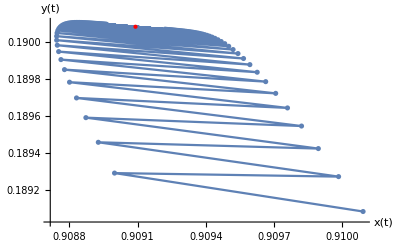

```mathematica
c=1.1;
r=2.3;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,1,100}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Joined->True,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

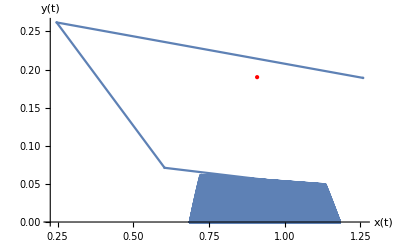

```mathematica
c=1.1;
r=2.3;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.35,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,1,1000}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Joined->True,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

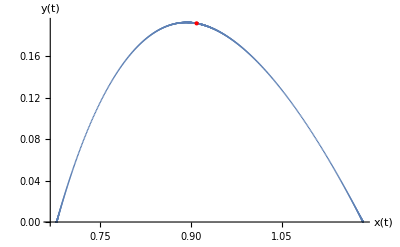

```mathematica
c=1.1;
r=2.32;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1/c+0.001,y[1]==r*(c-1)/(c^2)-0.001},{x,y},{t,1,5000}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

```mathematica
Clear[c]
```

```mathematica
Clear[r]
```

```mathematica
fv[x_,y_,a_,b_]:=(a+1)*x-a*x^2-b*x*y;
gv[x_,y_,a_,b_]:=b*x*y;
```

```mathematica
FindRoot[{x==fv[fv[x,y,2.28,1.1],gv[x,y,2.28,1.1],2.28,1.1],y==gv[fv[x,y,2.28,1.1],gv[x,y,2.28,1.1],2.28,1.1]},{{x,1.2},{y,0}}]
```

{x→1.17867,y→0.}

```mathematica
1/c
```

0.909091

```mathematica
r*(c-1)/(c^2)
```

0.18843

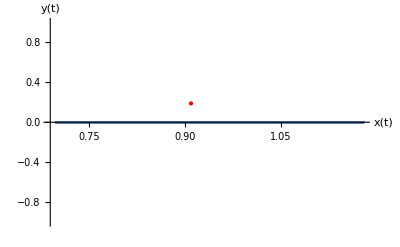

```mathematica
c=1.1;
r=2.28;
sol2=RecurrenceTable[{x[t+1]==(r+1)*x[t]-r*x[t]^2-c*x[t]*y[t],y[t+1]==c*x[t]*y[t],x[1]==1.1786654769018248,y[1]==0},{x,y},{t,1,10000}];
ListPlot[sol2,PlotRange->All,AxesLabel->{x[t],y[t]},Mesh->All,Joined->True,Epilog->{Red,PointSize[Medium],Point[{1/c,r*(c-1)/(c^2)}]}]
```

```mathematica
Clear[r]
```

```mathematica
Clear[c]
```

```mathematica
J={{D[fv[x,y,r,c],x],D[fv[x,y,r,c],y]},{D[gv[x,y,r,c],x],D[gv[x,y,r,c],y]}}
```

{{1+r-2 r x-c y,-c x},{c y,c x}}

```mathematica
MatrixForm[J]
```

(1+r-2 r x-c y | -c x
c y | c x)

```mathematica
MatrixForm[FullSimplify[J/.{x->1/c,y->r*(c-1)/(c^2)}]]
```

(1-r/c | -1
((-1+c) r)/c | 1)

```mathematica
Collect[CharacteristicPolynomial[J/.{x->1/c,y->r*(c-1)/(c^2)},s],s]
```

1+r-(2 r)/c+(-2+r/c) s+s^2

Primer condición



Segunda condición





Tercera condición